### Examples of random walk. by Hong-Yi Zhang, 201025.

#### 1D model: coin flip.

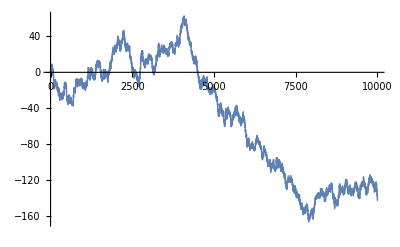

```mathematica
ListPlot[ NestList[ # + 2.(RandomInteger[] - 0.5)&, 0, 10000]]
```

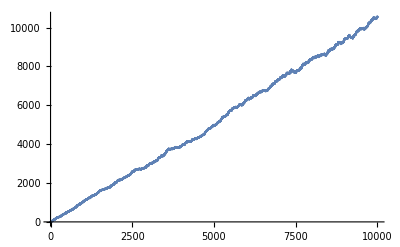

```mathematica
RW1D=Table[ NestList[ # + 2.(RandomInteger[] - 0.5)&, 0, 10000], {j, 1, 500}];
ListPlot@Mean[RW1D^2]
```

#### 2D model: drunkard walk.

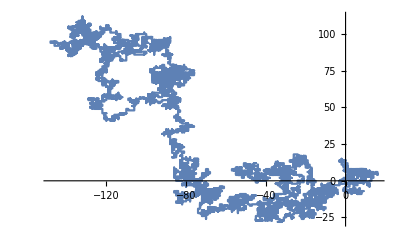

```mathematica
ListPlot[ NestList[ # + RandomChoice[{{1, 0}, {-1, 0}, {0, 1}, {0, -1}}]&, {0, 0}, 10000], Joined->True]
```

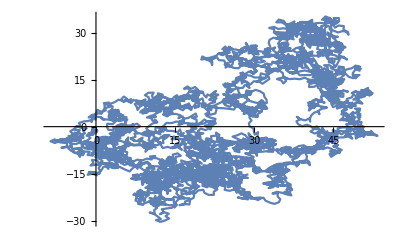

```mathematica
move := Module[ {phi=RandomReal[{0, 2π}]}, {Cos[phi],Sin[phi]}]
ListPlot[ NestList[ #+move&, {0, 0}, 5000], Joined->True]
```